```mathematica
in:={3,4,3,1,2}
counts:=Counts[in]/@Range[0,8]/.Missing->(0&)
counts
M:={{0,1,0,0,0,0,0,0,0},
{0,0,1,0,0,0,0,0,0},
{0,0,0,1,0,0,0,0,0},
{0,0,0,0,1,0,0,0,0},
{0,0,0,0,0,1,0,0,0},
{0,0,0,0,0,0,1,0,0},
{1,0,0,0,0,0,0,1,0},
{0,0,0,0,0,0,0,0,1},
{1,0,0,0,0,0,0,0,0}}
M//MatrixForm
Table[Dot[MatrixPower[M,n],counts]//{#,Total[#]}&,{n,0,18}]//MatrixForm
Table[n->Total@Dot[MatrixPower[M,n],counts],{n,{18,80,256}}]
MatrixPower[M,18]//MatrixForm
MatrixPower[M,80]//MatrixForm
MatrixPower[M,256]//MatrixForm
```

{0,1,1,2,1,0,0,0,0}

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

({0,1,1,2,1,0,0,0,0} | 5
{1,1,2,1,0,0,0,0,0} | 5
{1,2,1,0,0,0,1,0,1} | 6
{2,1,0,0,0,1,1,1,1} | 7
{1,0,0,0,1,1,3,1,2} | 9
{0,0,0,1,1,3,2,2,1} | 10
{0,0,1,1,3,2,2,1,0} | 10
{0,1,1,3,2,2,1,0,0} | 10
{1,1,3,2,2,1,0,0,0} | 10
{1,3,2,2,1,0,1,0,1} | 11
{3,2,2,1,0,1,1,1,1} | 12
{2,2,1,0,1,1,4,1,3} | 15
{2,1,0,1,1,4,3,3,2} | 17
{1,0,1,1,4,3,5,2,2} | 19
{0,1,1,4,3,5,3,2,1} | 20
{1,1,4,3,5,3,2,1,0} | 20
{1,4,3,5,3,2,2,0,1} | 21
{4,3,5,3,2,2,1,1,1} | 22
{3,5,3,2,2,1,5,1,4} | 26)

{18→26,80→5934,256→26984457539}

(1 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 2 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 2 | 0 | 1 | 0
0 | 1 | 0 | 0 | 1 | 0 | 2 | 0 | 1
3 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 0
0 | 3 | 0 | 1 | 0 | 0 | 1 | 0 | 2
2 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 1)

(252 | 20 | 210 | 37 | 120 | 84 | 45 | 126 | 11
56 | 252 | 20 | 210 | 37 | 120 | 84 | 45 | 126
210 | 56 | 252 | 20 | 210 | 37 | 120 | 84 | 45
165 | 210 | 56 | 252 | 20 | 210 | 37 | 120 | 84
121 | 165 | 210 | 56 | 252 | 20 | 210 | 37 | 120
330 | 121 | 165 | 210 | 56 | 252 | 20 | 210 | 37
57 | 330 | 121 | 165 | 210 | 56 | 252 | 20 | 210
210 | 37 | 120 | 84 | 45 | 126 | 11 | 126 | 9
20 | 210 | 37 | 120 | 84 | 45 | 126 | 11 | 126)

(655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774
659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910
697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547
869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865
757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368
1080854253 | 757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906
896132037 | 1080854253 | 757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885
589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774 | 315985166 | 215567357
496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774 | 315985166)

```mathematica
CharacteristicPolynomial[M,x]
```

1+x^2-x^9

```mathematica
Eigenvalues[M]
```

{Root1.09Root[-1-#1^2+#1^9&,1]1.0910244704807568,Root-0.996+0.417 ⅈRoot[-1-#1^2+#1^9&,3]-0.9961306220554406,Root-0.996-0.417 ⅈRoot[-1-#1^2+#1^9&,2]-0.9961306220554406,Root0.734+0.742 ⅈRoot[-1-#1^2+#1^9&,9]0.734077898463753,Root0.734-0.742 ⅈRoot[-1-#1^2+#1^9&,8]0.734077898463753,Root-0.379+0.893 ⅈRoot[-1-#1^2+#1^9&,5]-0.3792139806548107,Root-0.379-0.893 ⅈRoot[-1-#1^2+#1^9&,4]-0.3792139806548107,Root0.0958+0.870 ⅈRoot[-1-#1^2+#1^9&,7]0.09575446900611988,Root0.0958-0.870 ⅈRoot[-1-#1^2+#1^9&,6]0.09575446900611988}

FittedModel[ⅇ^(5.87419+0.0871767 x)]

ⅇ^(5.87419+0.0871767 x)

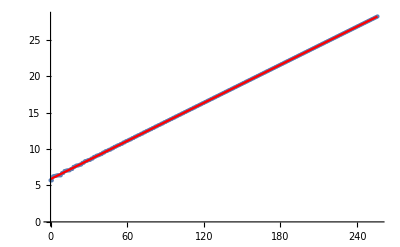

```mathematica
pts=Table[{n,Plus@@Dot[MatrixPower[M,n],counts]},{n,0,256}];
m=NonlinearModelFit[pts,Exp[a+b x],{a,b},x,MaxIterations->10000000000]
Normal[m]
logpts=Transpose@{pts[[All,1]],N@Log[pts[[All,2]]]};
Show[ListPlot[logpts,PlotStyle->PointSize[Medium]],Plot[Log[m[x]],{x,0,256},PlotStyle->Red]]
```

```mathematica
Total[Dot[MatrixPower[M,256],{x0,x1,x2,x3,x4,x5,x6,x7,x8}]]
```

6703087164 x0+6206821033 x1+5617089148 x2+5217223242 x3+4726100874 x4+4368232009 x5+3989468462 x6+3649885552 x7+3369186778 x8

```mathematica
poly[x0,x1,x2,x3,x4,x5,x6,x7,x8]:=6703087164 x0+6206821033 x1+5617089148 x2+5217223242 x3+4726100874 x4+4368232009 x5+3989468462 x6+3649885552 x7+3369186778 x8
Apply[poly][counts]
```

poly[0,212,23,25,21,19,0,0,0]

```mathematica
Total[Dot[MatrixPower[M,80],{x0,x1,x2,x3,x4,x5,x6,x7,x8}]]
```

1421 x0+1401 x1+1191 x2+1154 x3+1034 x4+950 x5+905 x6+779 x7+768 x8

```mathematica
poly:=Function[{x0,x1,x2,x3,x4,x5,x6,x7,x8},1421 x0+1401 x1+1191 x2+1154 x3+1034 x4+950 x5+905 x6+779 x7+768 x8]
```

```mathematica
Apply[poly][counts]
```

393019

```mathematica
p2:=Function[{x0,x1,x2,x3,x4,x5,x6,x7,x8},6703087164 x0+6206821033 x1+5617089148 x2+5217223242 x3+4726100874 x4+4368232009 x5+3989468462 x6+3649885552 x7+3369186778 x8]
Apply[p2][counts]
```

1757714216975

```mathematica
M//TraditionalForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
MatrixPower[M,80]//TraditionalForm
```

(252 | 20 | 210 | 37 | 120 | 84 | 45 | 126 | 11
56 | 252 | 20 | 210 | 37 | 120 | 84 | 45 | 126
210 | 56 | 252 | 20 | 210 | 37 | 120 | 84 | 45
165 | 210 | 56 | 252 | 20 | 210 | 37 | 120 | 84
121 | 165 | 210 | 56 | 252 | 20 | 210 | 37 | 120
330 | 121 | 165 | 210 | 56 | 252 | 20 | 210 | 37
57 | 330 | 121 | 165 | 210 | 56 | 252 | 20 | 210
210 | 37 | 120 | 84 | 45 | 126 | 11 | 126 | 9
20 | 210 | 37 | 120 | 84 | 45 | 126 | 11 | 126)

```mathematica
MatrixPower[M,256]//TraditionalForm
```

(655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774
659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910
697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547
869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368 | 357868865
757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906 | 491122368
1080854253 | 757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885 | 399865906
896132037 | 1080854253 | 757734771 | 869885915 | 697451775 | 659462321 | 655568076 | 496266131 | 589731885
589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774 | 315985166 | 215567357
496266131 | 589731885 | 399865906 | 491122368 | 357868865 | 378763547 | 339582910 | 280698774 | 315985166)

```mathematica
Total[Dot[MatrixPower[M,80],{x0,x1,x2,x3,x4,x5,x6,x7,x8}]]
```

1421 x0+1401 x1+1191 x2+1154 x3+1034 x4+950 x5+905 x6+779 x7+768 x8

```mathematica
Total[Dot[MatrixPower[M,256],{x0,x1,x2,x3,x4,x5,x6,x7,x8}]]
```

6703087164 x0+6206821033 x1+5617089148 x2+5217223242 x3+4726100874 x4+4368232009 x5+3989468462 x6+3649885552 x7+3369186778 x8